## Project 9 - Javier Salazar 1001144647.

Use the Metropolis-Hastings Algorithm to simulate samples  from distributions 1- 3  below for sample sizes  of  40,00  and  100,000.  Plot together simulated probability density histogram and π (x)  in all cases.

 1.  π (k )  =  27720/83711 1/(k+1) ,    k = 0, 1 , . . . , 10      
 Hint.  Use  symmetric random walk on {0,1, . . . , 10}  with sticky boundary at  {0} and {10} from Lab5_Notebook.

start = 5

sample size = 40000

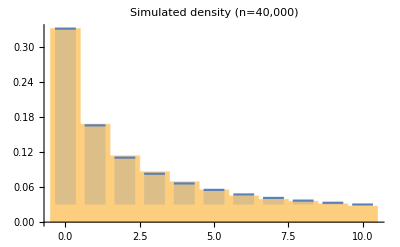

```mathematica
Clear[simu1,X,Y];
  X[0]=5;Print["start = ",X[0]];n=40000;
  Do[Which[0<X[k]<10,Y=X[k]+2RandomInteger[]-1;m=Min[1,(X[k]+1)/(Y+1)],
X[k]==0,Y=X[k]+RandomInteger[];m=Min[1,(X[k]+1)/(Y+1)],
X[k]==10,Y=X[k]+RandomInteger[]-1;m=Min[1,(X[k]+1)/(Y+1)]];
{U=RandomReal[],If[U≤m, X[k+1]=Y,X[k+1]=X[k]]},{k,0,n-1}];
  simu1=Table[X[k],{k,0,n-1}]; 
  Print["sample size = ",Length[simu1]];
   Show[Histogram[simu1,{-0.5,10.5,1},"ProbabilityDensity",PlotRange->All,PlotLabel->"Simulated density (n=40,000) "],
 DiscretePlot[27720/83711 1/(k+1),{k,0,10},ExtentSize->.7,PlotRange->All]]
```

start = 5

sample size = 100000

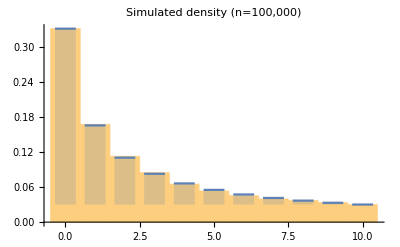

```mathematica
Clear[simu1,X,Y];
  X[0]=5;Print["start = ",X[0]];n=100000;
  Do[Which[0<X[k]<10,Y=X[k]+2RandomInteger[]-1;m=Min[1,(X[k]+1)/(Y+1)],
X[k]==0,Y=X[k]+RandomInteger[];m=Min[1,(X[k]+1)/(Y+1)],
X[k]==10,Y=X[k]+RandomInteger[]-1;m=Min[1,(X[k]+1)/(Y+1)]];
{U=RandomReal[],If[U≤m, X[k+1]=Y,X[k+1]=X[k]]},{k,0,n-1}];
  simu1=Table[X[k],{k,0,n-1}]; 
  Print["sample size = ",Length[simu1]];
   Show[Histogram[simu1,{-0.5,10.5,1},"ProbabilityDensity",PlotRange->All,PlotLabel->"Simulated density (n=100,000) "],
 DiscretePlot[27720/83711 1/(k+1),{k,0,10},ExtentSize->.7,PlotRange->All]]
```

2.   π (x)  =  cos(x)/2   for    -π/2 ≤  x  ≤ π/2

start = 0

a = 1

sample size = 40000

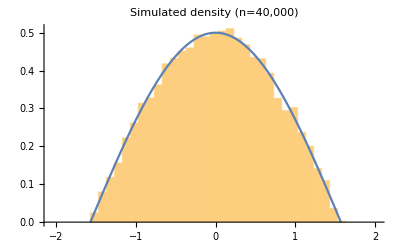

```mathematica
X[0]=0;Print["start = ",X[0]];n=40000;a=1;Print["a = ",a];
Do[{Y=RandomReal[{X[k]-a,X[k]+a}],U=RandomReal[],m=Min[1,Cos[Y]/Cos[X[k]]],
If[U≤m,X[k+1]=Y,X[k+1]=X[k]]},{k,0,n-1}];
simu1=Table[X[k],{k,0,n-1}];Print["sample size = ",Length[simu1]];
Show[Histogram[simu1,{-Pi/2-.5,Pi/2+.5,.1},"ProbabilityDensity",PlotRange->All,PlotLabel->"Simulated density (n=40,000)"],Plot[Cos[x]/2,{x,-Pi/2,Pi/2}, PlotRange->All]]
```

start = 0

a = 1

sample size = 100000

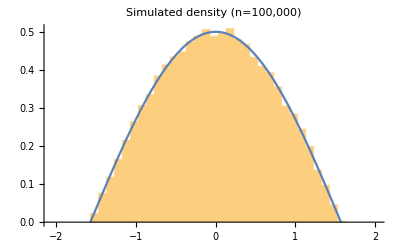

```mathematica
X[0]=0;Print["start = ",X[0]];n=100000;a=1;Print["a = ",a];
Do[{Y=RandomReal[{X[k]-a,X[k]+a}],U=RandomReal[],m=Min[1,Cos[Y]/Cos[X[k]]],
If[U≤m,X[k+1]=Y,X[k+1]=X[k]]},{k,0,n-1}];
simu1=Table[X[k],{k,0,n-1}];Print["sample size = ",Length[simu1]];
Show[Histogram[simu1,{-Pi/2-.5,Pi/2+.5,.1},"ProbabilityDensity",PlotRange->All,PlotLabel->"Simulated density (n=100,000)"],Plot[Cos[x]/2,{x,-Pi/2,Pi/2}, PlotRange->All]]
```

3.  π (x)  =   1/3 f(x)+2/3 g(x),    0 ≤  x  ≤  3 ,   is  a  convex mixture of densities  
       
  f(x)  =  3/4 x (2-x)   on   [0, 2]      and     g(x) =  3/4(x-1) (3-x)   on [1, 3]

```mathematica
f[x_]:= x (2-x)3/4/;x≤2 ∧ x≥0                
f[x_]:=0  /;(x>2 || x <0)
```

```mathematica
g[x_]:= (x-1) (3-x)3/4/;x≤3 ∧ x≥1                
g[x_]:=0  /;(x>3 || x <1)
```

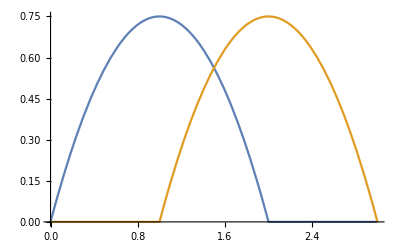

```mathematica
Plot[{f[x],g[x]},{x,0,3}]
```

```mathematica
h[x_]:=1/3 f[x]+2/3 g[x]   (* π(x) = h(x) *)
```

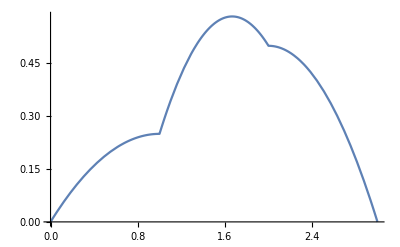

```mathematica
Plot[h[x],{x,0,3}]
```

start = 1.5

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of 1+Accepted.

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

sample size = 40000

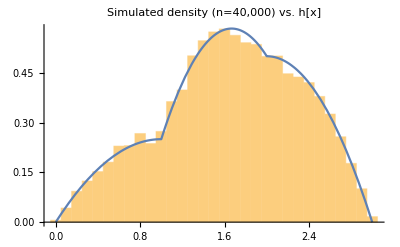

```mathematica
X[0]=1.5;Print["start = ",X[0]];n=40000;
Do[{Y=Random[NormalDistribution[X[k],1]],U=RandomReal[],m=Min[1,h[Y]/h[X[k]]],
If[U≤m,X[k+1]=Y;Accepted=Accepted+1,X[k+1]=X[k]]},{k,0,n-1}];
simu1=Table[X[k],{k,0,n-1}];Print["sample size = ",Length[simu1]];
Show[Histogram[simu1,{0-.05,3+.05,.1},"ProbabilityDensity",PlotRange->All,PlotLabel->"Simulated density (n=40,000) vs. h[x]"],Plot[h[x],{x,0,3}, PlotRange->All]]
```

start = 1.5

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of 1+Accepted.

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

sample size = 100000

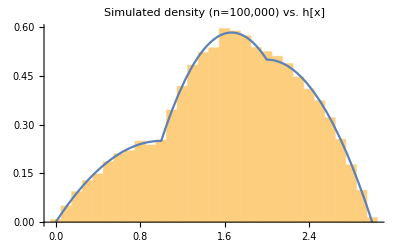

```mathematica
X[0]=1.5;Print["start = ",X[0]];n=100000;
Do[{Y=Random[NormalDistribution[X[k],1]],U=RandomReal[],m=Min[1,h[Y]/h[X[k]]],
If[U≤m,X[k+1]=Y;Accepted=Accepted+1,X[k+1]=X[k]]},{k,0,n-1}];
simu1=Table[X[k],{k,0,n-1}];Print["sample size = ",Length[simu1]];
Show[Histogram[simu1,{0-.05,3+.05,.1},"ProbabilityDensity",PlotRange->All,PlotLabel->"Simulated density (n=100,000) vs. h[x]"],Plot[h[x],{x,0,3}, PlotRange->All]]
```